```mathematica
L=4;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

25

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

If[1<t<2,0,0]+If[2<t<3,1,0]+If[3<t<4,0,0]+If[4<t<5,1,0]+If[5<t<6,1,0]+If[6<t<7,0,0]+If[7<t<8,1,0]+If[8<t<9,1,0]+If[9<t<10,1,0]+If[10<t<11,0,0]+If[11<t<12,0,0]+If[12<t<13,0,0]+If[13<t<14,1,0]+If[14<t<15,0,0]+If[15<t<16,0,0]+If[16<t<17,1,0]+If[17<t<18,0,0]+If[18<t<19,0,0]+If[19<t<20,1,0]+If[20<t<21,1,0]+If[21<t<22,0,0]+If[22<t<23,1,0]+If[23<t<24,1,0]+If[24<t<25,1,0]+If[25<t<26,1,0]

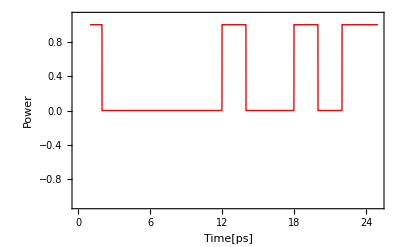

```mathematica
bit=25

digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,bit}]
step1[t_,i_]:=If[digital[i]==1,If[i<t<(i+1),1,0],If[i<t<(i+1),0,0]]
signal[t]:=∑_(i=1)^bit step1[t,i]
signal[t]
Plot[signal[t],{t,1,bit},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
```

Cos[400 π t]

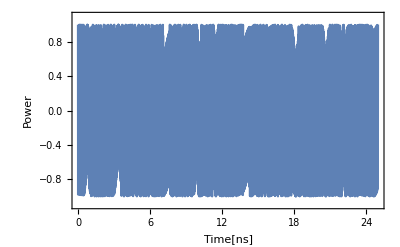

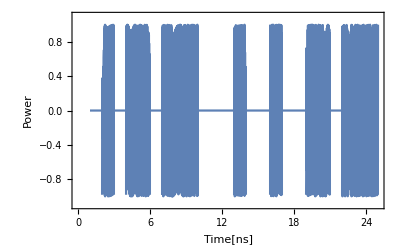

-Graphics-

(f Cos[36 f π] Sin[16 f π])/(2 (-40000+f^2) π)-(f Cos[8 f π] Cos[36 f π] Sin[16 f π])/((-40000+f^2) π)+(f Cos[12 f π] Cos[36 f π] Sin[16 f π])/((-40000+f^2) π)+(f Sin[36 f π])/(2 (-40000+f^2) π)-(f Cos[16 f π] Sin[36 f π])/(2 (-40000+f^2) π)+(f Cos[8 f π] Cos[16 f π] Sin[36 f π])/((-40000+f^2) π)-(f Cos[12 f π] Cos[16 f π] Sin[36 f π])/((-40000+f^2) π)+ⅈ ((f Cos[36 f π])/(2 (-40000+f^2) π)-(f Cos[16 f π] Cos[36 f π])/(2 (-40000+f^2) π)+(f Cos[8 f π] Cos[16 f π] Cos[36 f π])/((-40000+f^2) π)-(f Cos[12 f π] Cos[16 f π] Cos[36 f π])/((-40000+f^2) π)-(f Sin[16 f π] Sin[36 f π])/(2 (-40000+f^2) π)+(f Cos[8 f π] Sin[16 f π] Sin[36 f π])/((-40000+f^2) π)-(f Cos[12 f π] Sin[16 f π] Sin[36 f π])/((-40000+f^2) π))

```mathematica
Fc= 200 ;(*搬送波の周波数[THz]*)
carrier[t_]= Cos[2*Pi*Fc*t]
Plot[carrier[t], {t,0,25},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
cs[t_]:=signal[t]*carrier[t]

Plot[Evaluate[cs[t]],{t,1,bit},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
Plot[Evaluate[cs[t]],{t,1,bit},Frame->True,FrameLabel->{"Time[ns]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{-1.1,1.1}]
ComplexExpand[∫_0^(bit*25) cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
```

```mathematica
Evaluate[∫_0^bit cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1)ⅆt1]
ComplexExpand[Integratepaclet:ref/Integrate[cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,25}]]
Nintegrate[cs[t1]*ⅇ^(-ⅈ*2*Pi*f*t1),{t,0,25}]
```

(ⅈ ⅇ^(-36 ⅈ f π) f (1+ⅇ^(16 ⅈ f π) (-1+2 Cos[8 f π]-2 Cos[12 f π])))/(2 (-40000+f^2) π)

Rule::rhs: パターンpaclet:ref/Integrateは規則System`ComplexExpandDump`reimexpr[RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) Cos[400 π t1] (If[1<t1<2,0,0]+If[2<t1<3,0,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,0,0]+If[8<t1<9,0,0]+If[9<t1<10,0,0]+If[10<t1<11,1,0]+«15»),{t,0,25}]]→{RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) Cos[400 π t1] (If[1<t1<2,0,0]+«9»+«15»),{«1»}],0}の右辺にあります．

RefLink[Integrate,paclet:ref/Integrate][ⅇ^(-2 ⅈ f π t1) Cos[400 π t1] (If[1<t1<2,0,0]+If[2<t1<3,0,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,0,0]+If[8<t1<9,0,0]+If[9<t1<10,0,0]+If[10<t1<11,1,0]+If[11<t1<12,1,0]+If[12<t1<13,1,0]+If[13<t1<14,1,0]+If[14<t1<15,0,0]+If[15<t1<16,0,0]+If[16<t1<17,1,0]+If[17<t1<18,1,0]+If[18<t1<19,0,0]+If[19<t1<20,0,0]+If[20<t1<21,0,0]+If[21<t1<22,0,0]+If[22<t1<23,0,0]+If[23<t1<24,0,0]+If[24<t1<25,0,0]+If[25<t1<26,0,0]),{t,0,25}]

Nintegrate[ⅇ^(-2 ⅈ f π t1) Cos[400 π t1] (If[1<t1<2,0,0]+If[2<t1<3,0,0]+If[3<t1<4,0,0]+If[4<t1<5,1,0]+If[5<t1<6,1,0]+If[6<t1<7,0,0]+If[7<t1<8,0,0]+If[8<t1<9,0,0]+If[9<t1<10,0,0]+If[10<t1<11,1,0]+If[11<t1<12,1,0]+If[12<t1<13,1,0]+If[13<t1<14,1,0]+If[14<t1<15,0,0]+If[15<t1<16,0,0]+If[16<t1<17,1,0]+If[17<t1<18,1,0]+If[18<t1<19,0,0]+If[19<t1<20,0,0]+If[20<t1<21,0,0]+If[21<t1<22,0,0]+If[22<t1<23,0,0]+If[23<t1<24,0,0]+If[24<t1<25,0,0]+If[25<t1<26,0,0]),{t,0,25}]

```mathematica
Cs[f]=ComplexExpand[FourierTransform[cs[t],t,2*Pi*f]]
```

(f Cos[4 f π] Sin[2 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[2 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Sin[4 f π])/(√2 (-40000+f^2) π^(3/2))+(f Cos[8 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[10 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[16 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[22 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[24 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[28 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[30 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[34 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[38 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[40 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[48 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Sin[8 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Sin[10 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Sin[16 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Sin[22 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Sin[24 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Sin[28 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Sin[30 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Sin[34 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Sin[38 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Sin[40 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Sin[48 f π])/(2 √2 (-40000+f^2) π^(3/2))+ⅈ ((f Cos[4 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[2 f π] Cos[4 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π]^2)/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Cos[8 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Cos[10 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Cos[16 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Cos[22 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Cos[24 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Cos[28 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Cos[30 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Cos[34 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Cos[38 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Cos[4 f π] Cos[40 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Cos[4 f π] Cos[48 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[2 f π] Sin[4 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[4 f π]^2)/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[4 f π] Sin[8 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[4 f π] Sin[10 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[4 f π] Sin[16 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[4 f π] Sin[22 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[4 f π] Sin[24 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[4 f π] Sin[28 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[4 f π] Sin[30 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[4 f π] Sin[34 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[4 f π] Sin[38 f π])/(2 √2 (-40000+f^2) π^(3/2))-(f Sin[4 f π] Sin[40 f π])/(2 √2 (-40000+f^2) π^(3/2))+(f Sin[4 f π] Sin[48 f π])/(2 √2 (-40000+f^2) π^(3/2)))

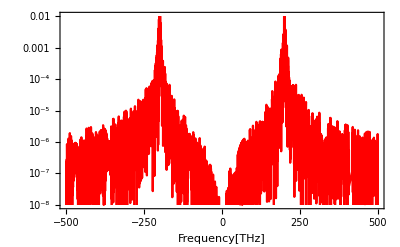

```mathematica
LogPlot[(Re[Cs[f]]^2+Im[Cs[f]]^2),{f,-0.5*10^3,0.5*10^3},Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{10^-8,10^-2},PlotStyle->{Red}]
```

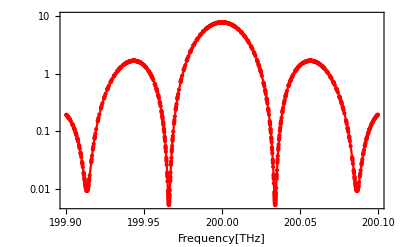

```mathematica
LogPlot[(Re[Cs[f]]^2+Im[Cs[f ]]^2),{f,1.999*10^2,2.001*10^2},Mesh->All,Frame->True,FrameLabel->{"Frequency[THz]"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,10},PlotStyle->{Red}]
```